```mathematica
f[x_] = (3x + π)/(√(1+ x^2 + √(1+x^2)^3))
```

(π+3 x)/(√(1+x^2+√((1+x^2)^3)))

```mathematica
a=0;b=6;n=10;x0=2.4316;h=(b-a)/n;
```

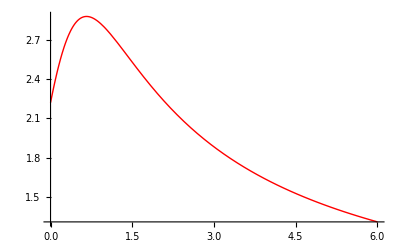

```mathematica
graph=Plot[f[x],{x,a,b},PlotStyle->{Red,Thick}]
```

```mathematica
data=Table[{i h,f[i h]},{i,0,n}]//N;
```

```mathematica
TableForm[data]
```

0. | 2.22144
0.6 | 2.87905
1.2 | 2.69633
1.8 | 2.37169
2.4 | 2.09635
3. | 1.88196
3.6 | 1.71455
4.2 | 1.58116
4.8 | 1.47253
5.4 | 1.38227
6. | 1.30598

```mathematica
listC=Table[0,{i,0,n}];
```

```mathematica
A=Table[0,{n-1},{n-1}];
```

```mathematica
Do[If[i≠1,A[[i,i-1]]=h];A[[i,i]]=4 h;If[i≠n-1,A[[i,i+1]]=h],{i,1,n-1}]
```

```mathematica
A//MatrixForm//N
```

(2.4 | 0.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.6 | 2.4)

```mathematica
B=Table[3 ((data[[i,2]]-data[[i-1,2]])/h-(data[[i-1,2]]-data[[i-2,2]])/h),{i,3,n+1}]//N;
```

```mathematica
X=LinearSolve[A,B];
```

```mathematica
For[i=1,i≤n-1,i++,listC[[i+1]]=X[[i]]];
```

```mathematica
MatrixForm[listC]
```

(0
-1.78571
0.140135
0.0423892
0.101204
0.0607507
0.0472582
0.0337362
0.0240902
0.0230589
0)

```mathematica
listA=Table[data[[i+1,2]],{i,1,n}]
```

{2.87905,2.69633,2.37169,2.09635,1.88196,1.71455,1.58116,1.47253,1.38227,1.30598}

```mathematica
listB=Table[(data[[i,2]]-data[[i-1,2]])/h+2/3 h listC[[i]]+1/3 h listC[[i-1]],{i,2,n+1}]
```

{0.381731,-0.605613,-0.496098,-0.409942,-0.31277,-0.247964,-0.199368,-0.164672,-0.136382,-0.122547}

```mathematica
listD=Table[(listC[[i]]-listC[[i-1]])/(3 h),{i,2,n+1}]
```

{-0.99206,1.06991,-0.0543034,0.0326747,-0.0224738,-0.00749581,-0.00751223,-0.00535891,-0.000572935,-0.0128105}

```mathematica
sData=Table[{listA[[i]]+listB[[i]] (x-data[[i+1,1]])+listC[[i+1]] (x-data[[i+1,1]])^2+listD[[i]] (x-data[[i+1,1]])^3,data[[i,1]]≤x≤data[[i+1,1]]}, {i,1,n}]//Simplify
```

{{2.22144+1.45316 x-0.99206 x^3,0.≤x≤0.6},{1.77606+3.68009 x-3.71155 x^2+1.06991 x^3,0.6≤x≤1.2},{3.7187-1.17653 x+0.335627 x^2-0.0543034 x^3,1.2≤x≤1.8},{3.21144-0.331101 x-0.134054 x^2+0.0326747 x^3,1.8≤x≤2.4},{3.97382-1.28407 x+0.263015 x^2-0.0224738 x^3,2.4≤x≤3.},{3.56941-0.879661 x+0.128213 x^2-0.00749581 x^3,3.≤x≤3.6},{3.57018-0.880299 x+0.12839 x^2-0.00751223 x^3,3.6≤x≤4.2},{3.41064-0.766345 x+0.101258 x^2-0.00535891 x^3,4.2≤x≤4.8},{2.88135-0.435539 x+0.0323404 x^2-0.000572935 x^3,4.8≤x≤5.4},{4.80833-1.50608 x+0.230589 x^2-0.0128105 x^3,5.4≤x≤6.}}

```mathematica
S[x_]=Piecewise[sData]
```

Piecewise[{{2.22144+1.45316 x-0.99206 x^3, 0.≤x≤0.6}, {1.77606+3.68009 x-3.71155 x^2+1.06991 x^3, 0.6≤x≤1.2}, {3.7187-1.17653 x+0.335627 x^2-0.0543034 x^3, 1.2≤x≤1.8}, {3.21144-0.331101 x-0.134054 x^2+0.0326747 x^3, 1.8≤x≤2.4}, {3.97382-1.28407 x+0.263015 x^2-0.0224738 x^3, 2.4≤x≤3.}, {3.56941-0.879661 x+0.128213 x^2-0.00749581 x^3, 3.≤x≤3.6}, {3.57018-0.880299 x+0.12839 x^2-0.00751223 x^3, 3.6≤x≤4.2}, {3.41064-0.766345 x+0.101258 x^2-0.00535891 x^3, 4.2≤x≤4.8}, {2.88135-0.435539 x+0.0323404 x^2-0.000572935 x^3, 4.8≤x≤5.4}, {4.80833-1.50608 x+0.230589 x^2-0.0128105 x^3, 5.4≤x≤6.}, {0, True}}]

```mathematica
graphD=ListPlot[data,PlotStyle->{Darker,PointSize[0.02]}];
```

```mathematica
graphS=Plot[S[x],{x,a,b}];
```

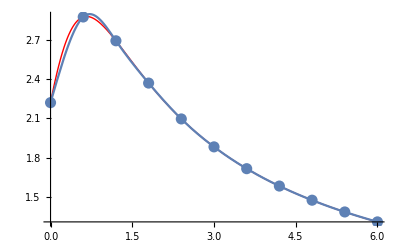

```mathematica
Show[graph,graphD,graphS]
```

```mathematica
Sf[x_]=Interpolation[data,x,Method->"Spline"]
```

InterpolatingFunction[…][x]

```mathematica
graphSf=Plot[Sf[x],{x,a,b}];
```

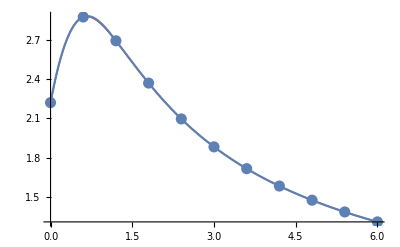

```mathematica
Show[graph,graphD,graphSf]
```

```mathematica
Needs["Splines`"]
```

```mathematica
Spl=SplineFit[data,Cubic]
```

SplineFunction[Cubic, {0.,10.}, <>]

```mathematica
t=(x-a)/h;
```

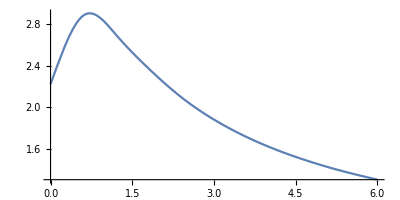

```mathematica
graphSpl=ParametricPlot[Spl[t],{t,0,n},AspectRatio->1/2]
```

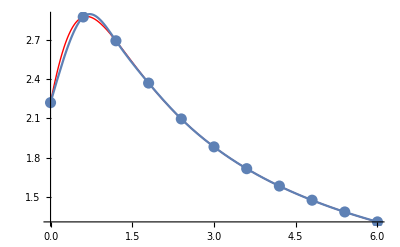

```mathematica
Show[graph,graphD,graphSpl]
```

```mathematica
Print["S[x0]=",S[x0]]
```

S[x0]=2.08349

```mathematica
Print["Sf[x0]=",Sf[x0]]
```

Sf[x0]=2.08361

```mathematica
Print["Spl[x0]=",Last[Spl[(x0-a)/h]]]
```

Spl[x0]=2.08349